```mathematica
norm[z_] := Re[z]^2 + Im[z]^2
```

```mathematica
iterationsToLeave[zr_, zi_, cr_, ci_]:=Module[{cnt,nz,nc},
nz=N[zr+zi I];
nc=N[cr + ci I];
cnt=0;
While[(cnt<100)&&(norm[nz]<10000),nz = nz^2 + nc;
cnt=cnt+1;];
cnt]
```

```mathematica
mandel=Function[{ans,n,c0,r,lim},Module[{dx=r/(n-1),dy=r/(n-1),z=I,c=I,k=1},ans=Table[z=0;c=c0+(2*i-1-n)*dx+(2*j-1-n)*I*dy;k=0;
While[Abs[z]<2&&k<lim,z=z^2+c;k++];k,{i,1,n},{j,1,n}]],{HoldFirst}];
```

```mathematica
iterationsToLeave[0,0,1,1/2]
```

5

```mathematica
fractaldata= Table[iterationsToLeave[0,0,x,y],{x,-3,1,0.2},{y,0,1,0.2}]
```

{{4,4,4,4,4,4},{4,4,4,4,4,4},{4,4,4,4,4,4},{5,5,4,4,4,4},{5,5,5,5,4,4},{100,6,5,5,5,4},{100,7,6,5,5,5},{100,7,6,6,5,5},{100,9,7,6,5,5},{100,21,10,7,6,5},{100,100,10,7,6,5},{100,18,10,8,7,6},{100,100,100,15,7,6},{100,100,100,28,9,7},{100,100,100,100,100,10},{100,100,100,100,21,100},{100,100,100,14,8,6},{9,34,12,18,7,6},{7,7,6,6,6,5},{6,6,5,5,5,5},{5,5,5,5,5,5}}

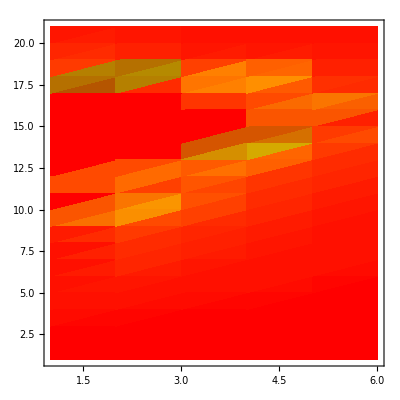

```mathematica
ListDensityPlot[fractaldata,ColorFunction->(Hue[#]&)]
```

```mathematica
fractalData[z0r_,z0i_,{{relMin_,relMax_},{imMin_,imMax_}},steps_]:=
{{{relMin,relMax},{imMin,imMax}},Table[iterationsToLeave[z0r,z0i,x,y],{y,imMin,imMax,(imMax-imMin)/steps},{x,relMin,relMax,(relMax-relMin)/steps} ]}
```

```mathematica
colorIt[x_]:= If[x==1,Hue[1,1,0], Hue[5x/6]]
```

```mathematica
fractalPlot[{{{relMin_,relMax_},{imMin_,imMax_}},data_}]:=ListDensityPlot[data,
DataRange->{{relMin,relMax},{imMin,imMax}},
Mesh->False,
Frame->False,
PlotRange->{1,100},
AspectRatio->1,
ColorFunction->(colorIt[#]&)]
```

```mathematica
fractaldata = fractalData[0,0,{{-3,1},{0,1}},200];
```

```mathematica
fractalPlot[fractaldata]
```

-Graphics-

```mathematica
compilediterToLeave = Compile[{zr,zi,cr,ci},Module[{cnt,temp,nzr,nzi,ncr,nci},nzr=N[zr];
nzi=N[zi];
ncr=N[cr];
nci=N[ci];
cnt=0;
While[(cnt<100)&&(nzr^2+nzi^2<10000),temp=nzr^2-nzi^2+ncr;
nzi=2 nzr nzi+nci;
nzr=temp;
cnt=cnt+1];
cnt]]
```

```mathematica
compilediterToLeave[0,0,1,1/2]
```

5

```mathematica
compiledFData[z0r_,z0i_,{{relMin_,relMax_},{imMin_,imMax_}},steps_]:={{{relMin,relMax},{imMin,imMax}},Table[compilediterToLeave[z0r,z0i,x,y],{y,imMin,imMax,(imMax-imMin)/steps},{x,relMin,relMax,(relMax-relMin)/steps}]}
```

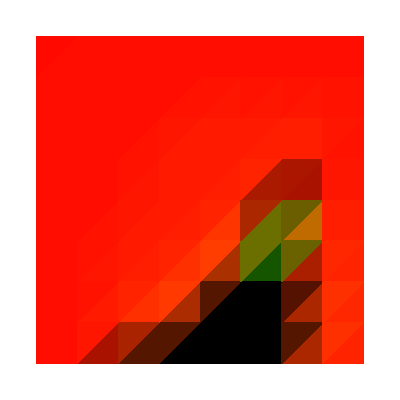
{0.016745,-Graphics-}

```mathematica
Timing[fractalPlot[fractalData[0,0,{{-3,1},{0,2}},8]]]
```

```mathematica
Timing[fractalPlot[compiledFData[0,0,{{-3,1},{0,2}},8]]]
```

{0.002888,-Graphics-}

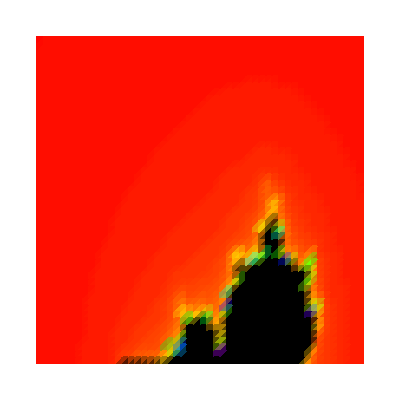
{0.382314,-Graphics-}

```mathematica
Timing[fractalPlot[fractalData[0,0,{{-3,1},{0,2}},50]]]
```

```mathematica
Timing[fractalPlot[compiledFData[0,0,{{-3,1},{0,2}},50]]]
```

{0.06867,-Graphics-}

```mathematica
Timing[fractalPlot[fractalData[0,0,{{-3,1},{0,2}},200]]]
```

{6.14275,-Graphics-}

```mathematica
Timing[fractalPlot[compiledFData[0,0,{{-3,1},{0,2}},200]]]
```

{1.25309,-Graphics-}